# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"DoubleBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis4.txt"}]];


LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_DB,Infinity];
```

# Generate Phase-Space Point

{d→227331725,mTsq→1596953085,s12→572974776,s16→1204651377,s345→294820535}

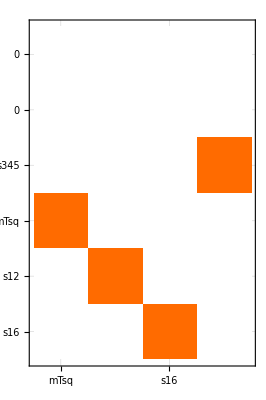

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
PureIntegralN=Expand[PureIntegrals/.tPoint/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P];
diffOp=getDifferentialOperator[tPoint];
epsrepl={(ep->(4-d)/2)/.tPoint};
checkDifferentialOperator[tPoint,diffOp]
```

# Compute Basis Change Matrix

0

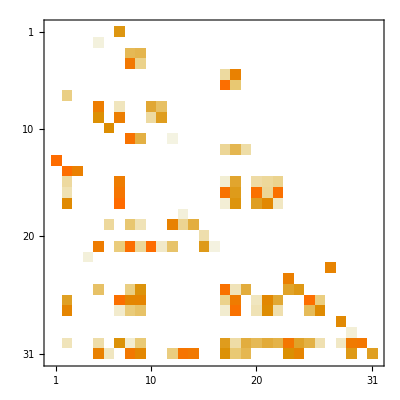

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/DB/numerics_2147483647_0.m"}]];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
Basis=Cases[PureIntegralN2,_DB,Infinity]//DeleteDuplicates;
NullInts=Thread[Rule[Complement[Basis,LaportaBasis],0]]//EchoFunction[Length];
PureIntegralN2=PureIntegralN2/.NullInts;
BasisChangMat=Table[CoefficientArrays[Expand[PureIntegralN2/.epsrepl,Modulus->$P][[pos]],LaportaBasis],{pos,1,31}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[Delete[{1,2,3,4,5},var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],ProgressIndicator[(var-1)*31+intpos,{1,31*6}]];
```

## Extra Step If Redu List does not exits yet

```mathematica
ToReduce=Cases[diffInts,_DB,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

242

```mathematica
ToReduce2=Cases[PureIntegralN,_DB,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
```

32

```mathematica
WriteJobFile[{"UReduList","ReduList"}]
```

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_DB,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,LaportaBasis];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

37

# Compute DE Matrices

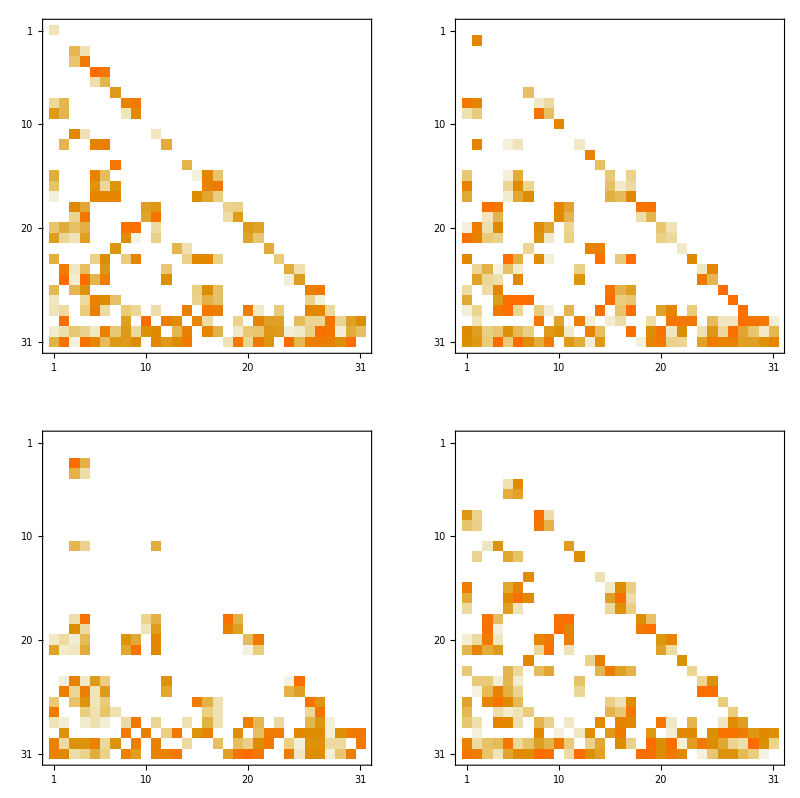

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],LaportaBasis]/.{0}->{0,ConstantArray[0,31]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[LaportaBasis]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2},{Mplot3,Mplot4}}]
```

```mathematica
LaportaBasis
```

{DB[0,1,0,0,1,0,1,0,0],DB[1,0,1,0,1,0,1,0,0],DB[0,1,1,0,1,0,1,0,0],DB[1,1,1,0,1,0,1,0,0],DB[0,1,0,1,1,0,0,0,0],DB[0,0,1,1,1,0,0,0,0],DB[0,1,1,1,1,0,0,0,0],DB[-1,1,1,1,1,0,0,0,0],DB[0,1,0,1,0,0,1,0,0],DB[-1,1,0,1,0,0,1,0,0],DB[1,1,0,1,0,0,1,0,0],DB[0,1,0,1,1,0,1,0,0],DB[-1,1,0,1,1,0,1,0,0],DB[0,1,-1,1,1,0,1,0,0],DB[0,1,1,1,1,0,1,0,0],DB[0,1,0,1,0,1,0,0,0],DB[-1,1,0,1,0,1,0,0,0],DB[1,0,1,1,0,1,0,0,0],DB[0,1,1,1,0,1,0,0,0],DB[1,1,1,1,0,1,0,0,0],DB[1,1,1,1,-1,1,0,0,0],DB[0,1,1,1,1,1,0,0,0],DB[-1,1,1,1,1,1,0,0,0],DB[1,1,0,1,0,1,1,0,0],DB[1,1,0,1,-1,1,1,0,0],DB[0,1,0,1,1,1,1,0,0],DB[-1,1,0,1,1,1,1,0,0],DB[0,1,1,1,1,1,1,0,0],DB[1,1,1,1,1,1,1,0,0],DB[1,1,1,1,1,1,1,-1,0],DB[1,1,1,1,1,1,1,0,-1]}

```mathematica
BasisChangMat//MatrixForm
```

(0 | 0 | 0 | 0 | 1058739093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 198771646 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1154448254 | 785350780 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1153258658 | 319382342 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1946648689 | 1384021173 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 684453881 | 1947466523 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
589846407 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1871368641 | 1836013382 | 933058213 | 1897801998 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1528463315 | 884419431 | 2065672027 | 6754678 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 228410835 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 191746492 | 1884242094 | 0 | 1575917421 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 506742973 | 1306039250 | 434310455 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 764600572 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
525946550 | 0 | 1035925011 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
646011061 | 0 | 0 | 0 | 244439211 | 0 | 0 | 0 | 195534379 | 810302641 | 0 | 556980761 | 622268837 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
630857880 | 0 | 0 | 0 | 612479231 | 0 | 0 | 0 | 2074618422 | 72040925 | 0 | 1730475751 | 501236800 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1445140663 | 0 | 0 | 0 | 1111520743 | 0 | 0 | 0 | 1522624403 | 1773656630 | 0 | 473905513 | 1362142121 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 854893039 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 669514478 | 1946285741 | 818530124 | 1787582409 | 1292123334 | 489846483 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2012745010 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1207585890 | 1914159081 | 1749485987 | 1938225297 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1627886977 | 1817380747 | 0 | 858583733 | 0 | 0 | 146691758 | 797782911 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 854893039 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2042858270 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 46082677 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1023283818 | 0 | 0 | 1213362231 | 698161399 | 1657637164 | 0 | 0 | 0 | 0 | 1120613438 | 1129232827 | 0 | 0 | 0 | 0 | 0 | 0 | 401163966 | 161820402 | 0 | 0 | 0 | 0 | 0 | 0
1772277690 | 0 | 0 | 0 | 309374345 | 0 | 0 | 0 | 1514896926 | 2040191995 | 0 | 550489250 | 1672603730 | 0 | 0 | 447696255 | 1762277160 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1358365796 | 1083245342 | 0 | 0 | 0 | 0
2145004255 | 0 | 0 | 0 | 1927580337 | 0 | 0 | 0 | 780292159 | 1884465085 | 0 | 1892989158 | 14527267 | 0 | 0 | 1231626620 | 1343347030 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 616565443 | 1229323127 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1351730617 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1601265751 | 0 | 0
1120305073 | 0 | 0 | 0 | 1026986591 | 766889880 | 0 | 0 | 1909438922 | 1489685481 | 546066948 | 1447625921 | 1343940175 | 0 | 0 | 1993397628 | 2122012213 | 0 | 0 | 0 | 0 | 0 | 0 | 2082982301 | 1293361016 | 1706244914 | 75496041 | 552855968 | 181344417 | 1594627679 | 0
0 | 0 | 0 | 0 | 0 | 1032587361 | 0 | 0 | 909302619 | 967117460 | 396500050 | 0 | 0 | 0 | 0 | 41194279 | 1890216066 | 2007940761 | 862649698 | 701512837 | 793000100 | 0 | 0 | 120785974 | 1959788909 | 0 | 0 | 0 | 501923513 | 0 | 474063366)

```mathematica
LaportaBasis2=Cases[reductionRules[[All,2]],_DB,Infinity]//DeleteDuplicates
```

{DB[1,0,1,0,1,0,1,0,0],DB[0,1,0,0,1,0,1,0,0],DB[0,1,1,0,1,0,1,0,0],DB[1,1,1,0,1,0,1,0,0],DB[0,0,1,1,1,0,0,0,0],DB[1,0,1,1,0,1,0,0,0],DB[0,1,0,1,1,0,0,0,0],DB[-1,1,0,1,0,1,0,0,0],DB[0,1,0,1,0,1,0,0,0],DB[-1,1,1,1,1,0,0,0,0],DB[0,1,1,1,1,0,0,0,0],DB[0,1,1,1,0,1,0,0,0],DB[1,1,1,1,-1,1,0,0,0],DB[1,1,1,1,0,1,0,0,0],DB[-1,1,1,1,1,1,0,0,0],DB[0,1,1,1,1,1,0,0,0],DB[-1,1,0,1,0,0,1,0,0],DB[0,1,0,1,0,0,1,0,0],DB[1,1,0,1,0,0,1,0,0],DB[-1,1,0,1,1,0,1,0,0],DB[0,1,0,1,1,-1,1,0,0],DB[0,1,0,1,1,0,1,0,0],DB[1,1,0,1,-1,1,1,0,0],DB[1,1,0,1,0,1,1,0,0],DB[-1,1,0,1,1,1,1,0,0],DB[0,1,0,1,1,1,1,0,0],DB[0,1,1,1,1,0,1,0,0],DB[0,1,1,1,1,1,1,0,0],DB[1,1,1,1,1,1,1,-1,0],DB[1,1,1,1,1,1,1,0,-1],DB[1,1,1,1,1,1,1,0,0]}

```mathematica
LaportaBasis
```

{DB[0,1,0,0,1,0,1,0,0],DB[1,0,1,0,1,0,1,0,0],DB[0,1,1,0,1,0,1,0,0],DB[1,1,1,0,1,0,1,0,0],DB[0,1,0,1,1,0,0,0,0],DB[0,0,1,1,1,0,0,0,0],DB[0,1,1,1,1,0,0,0,0],DB[-1,1,1,1,1,0,0,0,0],DB[0,1,0,1,0,0,1,0,0],DB[-1,1,0,1,0,0,1,0,0],DB[1,1,0,1,0,0,1,0,0],DB[0,1,0,1,1,0,1,0,0],DB[-1,1,0,1,1,0,1,0,0],DB[0,1,-1,1,1,0,1,0,0],DB[0,1,1,1,1,0,1,0,0],DB[0,1,0,1,0,1,0,0,0],DB[-1,1,0,1,0,1,0,0,0],DB[1,0,1,1,0,1,0,0,0],DB[0,1,1,1,0,1,0,0,0],DB[1,1,1,1,0,1,0,0,0],DB[1,1,1,1,-1,1,0,0,0],DB[0,1,1,1,1,1,0,0,0],DB[-1,1,1,1,1,1,0,0,0],DB[1,1,0,1,0,1,1,0,0],DB[1,1,0,1,-1,1,1,0,0],DB[0,1,0,1,1,1,1,0,0],DB[-1,1,0,1,1,1,1,0,0],DB[0,1,1,1,1,1,1,0,0],DB[1,1,1,1,1,1,1,0,0],DB[1,1,1,1,1,1,1,-1,0],DB[1,1,1,1,1,1,1,0,-1]}

```mathematica
Complement[LaportaBasis,LaportaBasis2]
Complement[LaportaBasis2,LaportaBasis]
```

{DB[0,1,-1,1,1,0,1,0,0]}

{DB[0,1,0,1,1,-1,1,0,0]}

```mathematica
Complement[LaportaBasis,LaportaBasis2]
```

```mathematica
Propagators={(k[1])^2,(k[1]+p[1])^2-mTsq,(k[1]+p[1]+p[2])^2,(k[1]+k[2])^2,(k[2])^2,(k[2]+p[4])^2,(k[2]+p[4]+p[3])^2,(k[1]+p[3])^2,(k[2]-p[1])^2};
```

```mathematica
Propagators/.{k[1]->k[1]-p[1]+p[4],k[2]->k[2]-p[3]+p[2]}/.p4cons
```

{(k[1]-2 p[1]-p[2]-p[3])^2,-mTsq+(k[1]-p[1]-p[2]-p[3])^2,(k[1]-p[1]-p[3])^2,(k[1]+k[2]-2 p[1]-2 p[3])^2,(k[2]+p[2]-p[3])^2,(k[2]-p[1]-2 p[3])^2,(k[2]-p[1]-p[3])^2,(k[1]-2 p[1]-p[2])^2,(k[2]-p[1]+p[2]-p[3])^2}